```mathematica
list = {{a,b,c,d,e},{f,g,h,j,k}}
list2 = {{a,b},{c,d}}
list3 = {{a,b,c},{d,e,f},{g,h,i}}
```

{{a,b,c,d,e},{f,g,h,j,k}}

{{a,b},{c,d}}

{{a,b,c},{d,e,f},{g,h,i}}

```mathematica
rrlist = RotateRight[list,2]
rrlist2 = RotateRight[list2,1]
rrlist3 = RotateRight[list3,2]
```

{{a,b,c,d,e},{f,g,h,j,k}}

{{c,d},{a,b}}

{{d,e,f},{g,h,i},{a,b,c}}

```mathematica
trrlist = Transpose[rrlist, 2]
```

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{d,e,a,b,c},2].

Transpose[{d,e,a,b,c},2]

```mathematica
ddx
```

{{1.08149,1.04367,1.23836,1.37635,1.09211,1.09446,1.09034,242,1.34989,1.44053,1.38187,1.49014,1.43446,1.30048,1.45758},254,{1}}
 |  |  |  |

```mathematica
gmx = GaussianMatrix[gfilt]
```

{{0.002589,0.0107788,0.0241466,0.0107788,0.002589},{0.0107788,0.0448755,0.10053,0.0448755,0.0107788},{0.0241466,0.10053,0.225206,0.10053,0.0241466},{0.0107788,0.0448755,0.10053,0.0448755,0.0107788},{0.002589,0.0107788,0.0241466,0.0107788,0.002589}}

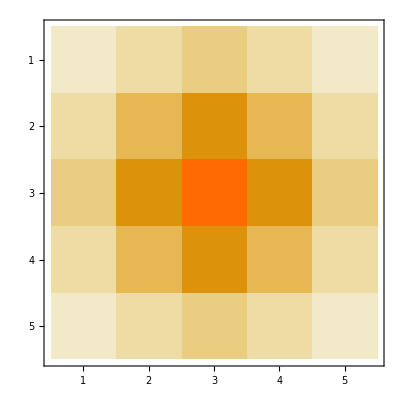

```mathematica
MatrixPlot[gmx]
```

```mathematica
ListCorrelate[gmx, ddx]
```

{{1.12123,1.09051,1.06823,1.07552,1.10586,1.15152,1.1171,238,1.37465,1.39195,1.39311,1.39198,1.37439,1.39228,1.42204},250,{1}}
 |  |  |  |

```mathematica
lcgmx = ListCorrelate[gmx,ddx,{1}]
```

{{1.12123,1.09051,1.06823,1.07552,1.10586,1.15152,1.1171,242,1.37439,1.39228,1.42204,1.37975,1.33532,1.19905,1.13565},254,{1}}
 |  |  |  |

```mathematica
Dimensions[ListCorrelate[gmx, ddx]]
Dimensions[lcgmx]
```

{252,252}

{256,256}

```mathematica
rrlcgmx=RotateRight[lcgmx,2]
```

{{1.17939,1.1974,1.14475,1.10988,1.12059,1.14089,1.09597,242,1.33209,1.36546,1.35335,1.29402,1.26834,1.17139,1.1501},254,{1}}
 |  |  |  |